# Derivation of p(x|I_1) for J=4

```mathematica
J=n=4;
```

```mathematica
Solve[r==Log[x/c]&&s==Log[y/x]&&t==Log[z/y]&&u==Log[w/z]&&0<c<x≤y≤z≤w,{x,y,z,w},PositiveReals]//FullSimplify
a={c ⅇ^r,c ⅇ^(r+s) ,c ⅇ^(r+s+t),c ⅇ^(r+s+t+u)};
b={r,s,t,u};
J=Det[Grad[a,b]]//FullSimplify
```

{{x→ConditionalExpression[c ⅇ^r,c>0&&r>0&&s>0&&t>0&&u>0],y→ConditionalExpression[c ⅇ^(r+s),c>0&&r>0&&s>0&&t>0&&u>0],z→ConditionalExpression[c ⅇ^(r+s+t),c>0&&r>0&&s>0&&t>0&&u>0],w→ConditionalExpression[c ⅇ^(r+s+t+u),c>0&&r>0&&s>0&&t>0&&u>0]}}

c^4 ⅇ^(4 r+3 s+2 t+u)

```mathematica
m[u_]:=Exp[u.Join[{0},Range[Length[u]-1]//Reverse]]
m[{r,s,t,u}]
```

ⅇ^(3 s+2 t+u)

```mathematica
Z[λ_]:=Integrate[m[{r,s,t,u}] Exp[-{r,s,t,u}.λ],{r,0,∞},{s,0,∞},{t,0,∞},{u,0,∞},Assumptions->λ∈Vectors[n,Reals]&&ρ>0]//FullSimplify
Z[{ρ,σ,τ,υ}]
```

1/(ρ (-3+σ) (-2+τ) (-1+υ))

```mathematica
(* Show that ρ is indeed positive, as we assumed in the integral *)
Assuming[ρ>0,D[Log[Z[{ρ,σ,τ,υ}]],{{ρ,σ,τ,υ},1}]==-{mr,ms,mt,mu}]
MEsolution=Solve[%,{mr,ms,mt,mu}][[1]]
```

{-1/ρ,-1/(-3+σ),-1/(-2+τ),-1/(-1+υ)}=={-mr,-ms,-mt,-mu}

{mr→1/ρ,ms→1/(-3+σ),mt→1/(-2+τ),mu→1/(-1+υ)}

The canonical ME solutions show the constraints on the Lagrange multipliers: ρ>0,σ>3,τ>2,υ>1.

```mathematica
p[u_,λ_]:=(1/Z[λ]) m[u] Exp[-u.λ] (*Boole[AllTrue[u,0<#&]]*)
p[{r,s,t,u},{ρ,σ,τ,υ}]
```

ⅇ^(3 s+2 t+u-r ρ-s σ-t τ-u υ) ρ (-3+σ) (-2+τ) (-1+υ)

```mathematica
Integrate[p[{r,s,t,u},{ρ,σ,τ,υ}],{r,0,∞},{s,0,∞},{t,0,∞},{u,0,∞},Assumptions->ρ>0]
```

1

## Derive joint distribution and marginals

```mathematica
q[x_,y_,z_,w_,c_,ρ_,σ_,τ_,υ_]:=p[{Log[x/c],Log[y/x],Log[z/y],Log[w/z]},{ρ,σ,τ,ν}]/(x y z w) Boole[0<c≤x≤y≤z≤w]
q[x,y,z,w,c,ρ,σ,τ,ν]//FullSimplify
```

Piecewise[{{c^ρ w^-ν x^(-4-ρ+σ) y^(-σ+τ) z^(ν-τ) (-1+ν) ρ (-3+σ) (-2+τ), c>0&&c≤x&&x≤y&&y≤z&&w≥z}, {0, True}}]

```mathematica
Integrate[q[x,y,z,w,c,ρ,σ,τ,ν],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},{w,-∞,∞},Assumptions->c>0&&ρ>0]
```

1

Use the constraints on the Lagrange multipliers derived above to drastically improve MMA's performance on these integrals.

```mathematica
px[x_,c_,ρ_,σ_,τ_,υ_]=Integrate[q[x,y,z,w,c,ρ,σ,τ,υ],{y,-∞,∞},{z,-∞,∞},{w,-∞,∞},Assumptions->0<c&&ρ>0&&σ>3&&τ>2&&υ>1]//FullSimplify
py[y_,c_,ρ_,σ_,τ_,υ_]=Integrate[q[x,y,z,w,c,ρ,σ,τ,υ],{x,-∞,∞},{z,-∞,∞},{w,-∞,∞},Assumptions->0<c&&ρ>0&&σ>3&&τ>2&&υ>1]//FullSimplify
pz[z_,c_,ρ_,σ_,τ_,υ_]=Integrate[q[x,y,z,w,c,ρ,σ,τ,υ],{x,-∞,∞},{y,-∞,∞},{w,-∞,∞},Assumptions->0<c&&ρ>0&&σ>3&&τ>2&&υ>1]//FullSimplify
pw[w_,c_,ρ_,σ_,τ_,υ_]=Integrate[q[x,y,z,w,c,ρ,σ,τ,υ],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->0<c&&ρ>0&&σ>3&&τ>2&&υ>1]//FullSimplify
```

Piecewise[{{c^ρ x^(-1-ρ) ρ, c>0&&c≤x}, {0, True}}]

Piecewise[{{(y^(-1-ρ-σ) (c^σ y^(3+ρ)-c^(3+ρ) y^σ) ρ (-3+σ))/(c^3 (3+ρ-σ)), c>0&&c<y}, {0, True}}]

Piecewise[{{(z^(-1-ρ-σ-τ) ρ (-3+σ) (-2+τ) (c^(1+τ) z^(2+ρ+σ) (3+ρ-σ)+c^(3+ρ) z^(σ+τ) (-1+σ-τ)+c^σ z^(3+ρ+τ) (-2-ρ+τ)))/(c^3 (3+ρ-σ) (2+ρ-τ) (-1+σ-τ)), c>0&&c<z}, {0, True}}]

Piecewise[{{(-1+ν) ρ (-3+σ) (-2+τ) (-(c^(-1+ν) w^-ν)/((-1+ν-ρ) (2+ν-σ) (1+ν-τ))+(c^ρ w^(-1-ρ))/((-1+ν-ρ) (3+ρ-σ) (2+ρ-τ))+(c^(-3+σ) w^(2-σ))/((2+ν-σ) (-3-ρ+σ) (-1+σ-τ))+((c/w)^τ w)/(c^2 (1+ν-τ) (-2-ρ+τ) (1-σ+τ))), c>0&&c<w}, {0, True}}]

For the moments to exist, the constraints on the Lagrange multipliers are made tighter by unit: ρ>0 turns into ρ>1, σ>3→σ>4, and so on.

```mathematica
Ex=Integrate[x px[x,c,ρ,σ,τ,υ],{x,-∞,∞},Assumptions->0<c&&ρ>1&&σ>4&&τ>3&&υ>2]//FullSimplify
Ey=Integrate[y py[y,c,ρ,σ,τ,υ],{y,-∞,∞},Assumptions->0<c&&ρ>1&&σ>4&&τ>3&&υ>2]//FullSimplify
Ez=Integrate[z pz[z,c,ρ,σ,τ,υ],{z,-∞,∞},Assumptions->0<c&&ρ>1&&σ>4&&τ>3&&υ>2]//FullSimplify
Ew=Integrate[w pw[w,c,ρ,σ,τ,υ],{w,-∞,∞},Assumptions->0<c&&ρ>1&&σ>4&&τ>3&&υ>2]//FullSimplify
```

(c ρ)/(-1+ρ)

(c ρ (-3+σ))/((-1+ρ) (-4+σ))

(c ρ (-3+σ) (-2+τ))/((-1+ρ) (-4+σ) (-3+τ))

(c (-1+ν) ρ (-3+σ) (-2+τ))/((-2+ν) (-1+ρ) (-4+σ) (-3+τ))

## Solve for Lagrange multipliers given formant frequency first moments

It is seen that the solutions automatically enforce the constraints on the Lagrange multipliers that allowed the moments to exist in the first place. This is logical: since we assert the first moments, our ME distribution better allows them to exist. Since these enforced constraints are stricter than those implied by the ME solutions in terms of first moments of u and those necessary for Z(λ) to exist, everything is well-defined.

```mathematica
mcond=0<c<mF1<mF2<mF3<mF4;
```

```mathematica
(* There was something weird with the ν symbol here -- check this first if there is a weird error *)
sol=Refine[Solve[mF1==Ex&&mF2==Ey&&mF3==Ez&&mF4==Ew&&mcond&&ρ>1&&σ>4&&τ>3&&ν>2,{ρ,σ,τ,ν},Reals],mcond][[1]]//FullSimplify
```

{ρ→mF1/(-c+mF1),σ→4+mF1/(-mF1+mF2),τ→3+mF2/(-mF2+mF3),ν→2+mF3/(-mF3+mF4)}

## Plots

Marginals p(x_i|c,μ_(1:i)) are identical for any n≥i given the same information c,μ_(1:i). So indeed knowledge of higher formants does not influence the marginals of lower formant frequencies.

```mathematica
marginals={px[x,c,ρ,σ,τ,υ],py[y,c,ρ,σ,τ,υ],pz[z,c,ρ,σ,τ,υ],pw[w,c,ρ,σ,τ,υ]}/.{y->x,z->x,w->x}/.sol/.{c->200,mF1->500,mF2->1000,mF3->1500,mF4->2000}//N//FullSimplify
```

{Piecewise[{{11399.8/x^(8/3), 200.≤x}, {0., True}}],Piecewise[{{0., x≤200.}, {(-400000.+68399. x^(1/3))/x^3, True}}],Piecewise[{{0., x≤200.}, {(6.×10^7-1.2×10^6 x+153898. x^(4/3))/x^4, True}}],Piecewise[{{0., x≤200.}, {(-1.37143×10^10+x (2.4×10^8-2.4×10^6 x+263825. x^(4/3)))/x^5, True}}]}

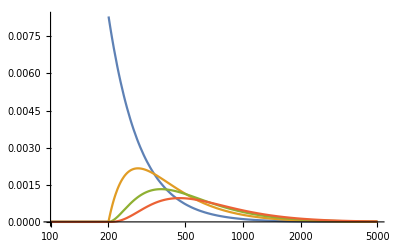

```mathematica
LogLinearPlot[marginals,{x,100,5000},PlotRange->Full]
```